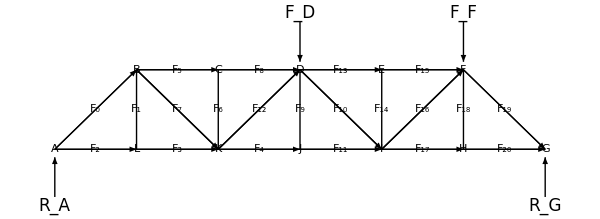

```mathematica
Module[{w,h,FD,FF,sol,RA,RG,scale,colC,colT},
w=5;h=5;
FD=10;FF=15;

sol=Quiet@Solve[{3*w*FD+5*w*FF-6*w*rg==0,ra+rg-FD-FF==0},{ra,rg}][[1]];
RG=rg/.sol;RA=ra/.sol;

scale[F_]:=Rescale[F,{0,15}];
colC=RGBColor[0,0.6,0];colT=RGBColor[1,0,0.25];

Graphics[{Thick,
{EdgeForm@Thick,FaceForm@None,Polygon[{{0,0},{6*w,0},{5*w,h},{w,h}}]},
Line[{{w,h},{2*w,0},{3*w,h},{4*w,0},{5*w,h}}],
Line[{{#*w,0},{#*w,h}}]&/@Range@5,

(*{Arrow[{#3,{#3[[1]],1.1*h}}],Text[Style[Subscript[Style["F",Italic],#2],17],#3,{0,-1.5}]}&@@@{{FD,"D",{3*w,h*(1.1+scale[FD])}},{FF,"F",{5*w,h*(1.1+scale[FF])}}},

{Arrow[{#3,{#3[[1]],-0.1*h}}],Text[Style[Subscript[Style["R",Italic],#2],17],#3,{0,1.5}]}&@@@{{RA,"A",{0,-h*(0.1+scale[RA])}},{RG,"G",{6*w,-h*(0.1+scale[RG])}}},*)

{Arrow[{{#3,1.6*h},{#3,1.1*h}}],Text[Style[Subscript[Style["F",Italic],#2],17],{#3,1.6*h},{0,-1.5}]}&@@@{{FD,"D",3*w},{FF,"F",5*w}},

{Arrow[{{#3,-0.6*h},{#3,-0.1*h}}],Text[Style[Subscript[Style["R",Italic],#2],17],{#3,-0.6*h},{0,1.5}]}&@@@{{RA,"A",0},{RG,"G",6*w}},

{Arrowheads@{{-0.035,0.1},{0.035,0.9}},
Arrow[{{0,0},{w,h}}],Arrow[{{#*w,h},{(#+1)*w,h}}]&/@Range@4,Arrow[{{5*w,h},{6*w,0}}],Arrow[{{2*w,0},{3*w,h}}],Arrow[{{3*w,h},{4*w,0}}]},

{Arrowheads@{{0.035,0.35},{-0.035,0.65}},
Arrow[{{#*w,0},{(#+1)*w,0}}]&/@Range[0,5],Arrow[{{w,h},{2*w,0}}],Arrow[{{4*w,0},{5*w,h}}]},

Text[Framed[Style[Subscript[Style["F",Italic],#1],18],Background->White,FrameStyle->None,FrameMargins->Tiny],#2]&@@@{
{0,{0.5*w,0.5*h}},{1,{w,0.5*h}},{2,{0.5*w,0}},{3,{1.5*w,0}},{4,{2.5*w,0}},{5,{1.5*w,h}},{6,{2*w,0.5*h}},{7,{1.5*w,0.5*h}},{8,{2.5*w,h}},{9,{3*w,0.5*h}},{10,{3.5*w,0.5*h}},{11,{3.5*w,0}},{12,{2.5*w,0.5*h}},{13,{3.5*w,h}},{14,{4*w,0.5*h}},{15,{4.5*w,h}},{16,{4.5*w,0.5*h}},{17,{4.5*w,0}},{18,{5*w,0.5*h}},{19,{5.5*w,0.5*h}},{20,{5.5*w,0}}},

Text[Framed[Style[Row@{" ",#1," "},16],Background->White,RoundingRadius->15,FrameMargins->Tiny],#2]&@@@{
{"A",{0,0},{1,0}},{"B",{w,h},{0,-1}},{"C",{2*w,h},{0,-1}},{"D",{3*w,h},{1,-1}},{"E",{4*w,h},{0,-1}},{"F",{5*w,h},{-1,-1}},{"G",{6*w,0},{-1,0}},{"H",{5*w,0},{0,1}},{" I ",{4*w,0},{0,1}},{"J",{3*w,0},{0,1}},{"K",{2*w,0},{0,1}},{"L",{w,0},{0,1}}}
},ImageSize->600]
]
```